```mathematica
(*Multistrain R0 analysis—Works with symbolic and numeric parameters*)
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];SetOptions[$FrontEndSession,NotebookAutoSave->True];
NotebookSave[];
AppendTo[$Path,FileNameJoin[{$HomeDirectory,"Dropbox","EpidCRNmodels"}]];
<<EpidCRN`;
(*===TEST CASE===*)

vars={s,i1,i2,i12};
rts={s0*mu0,mu1*s0^(-1)*R1*s*i1,mu2*s0^(-1)*R2*s*i2,mu3*s0^(-1)*R3*s*i12,ga1*i1*i2,ga2*i1*i2,et1*i1*i12,et2*i2*i12,be1*s*i12,be2*s*i12,mu0*s,mu1*i1,mu2*i2,mu3*i12};
RN={0->"s","s"+"i1"->2*"i1","s"+"i2"->2*"i2","s"+"i12"->2*"i12","i1"+"i2"->"i2"+"i12","i1"+"i2"->"i1"+"i12","i1"+"i12"->2*"i12","i2"+"i12"->2*"i12","s"+"i12"->"i1"+"i12","s"+"i12"->"i2"+"i12","s"->0,"i1"->0,"i2"->0,"i12"->0};
{spe, al, be, stoich, Rv, RHS,mSi, {defFormula, defTerms, defResult}}=extMat[RN];
{RHS, var, par, cp, mSi, Jx, Jy, E0, K, R0A, infV,ngm}=bdAn[RN,rts];
inf={2,3,4}; (*Indices of infected variables i1,i2,i12*)
K//MatrixForm
```

Load CRNT

((R1 s)/s0 | (be1 s)/mu3 | 0
0 | (R3 s)/s0 | 0
0 | (be2 s)/mu3 | (R2 s)/s0)

```mathematica
(*R0 analysis from existing K matrix-assumes EpidCRN package loaded*)(*Find SCCs from symbolic or numeric matrix*)findSCCs[Kmat_,params_,threshold_:10^-12]:=Module[{n,adj,G,reachable,sccs,unvisited,v,scc},n=Length[Kmat];
(*Build adjacency*)adj=Table[Module[{entry=Simplify[Kmat[[i,j]],Assumptions->And@@Thread[params>0]]},If[NumericQ[entry],If[Abs[entry]>threshold,1,0],If[entry=!=0,1,0]]],{i,n},{j,n}];
(*Build directed graph*)G=AdjacencyGraph[adj,DirectedEdges->True];
(*Compute reachability matrix*)reachable=Table[If[i==j,True,GraphDistance[G,i,j,Method->"Dijkstra"]<Infinity],{i,n},{j,n}];
(*Find SCCs*)sccs={};
unvisited=Range[n];
While[unvisited!={},v=First[unvisited];
scc=Select[unvisited,reachable[[v,#]]&&reachable[[#,v]]&];
AppendTo[sccs,scc];
unvisited=Complement[unvisited,scc];];
{sccs,adj,G,reachable}];

(*Compute R0 from K matrix and SCCs*)
computeR0[Kmat_,sccs_,params_,numeric_:False]:=Module[{blockRhos,R0},If[numeric,(*Numeric:use eigenvalues*)blockRhos=Table[Max[Abs[Eigenvalues[Kmat[[sccs[[k]],sccs[[k]]]]]]],{k,Length[sccs]}];
R0=Max[blockRhos];,(*Symbolic*)blockRhos=Table[Module[{block=Kmat[[sccs[[k]],sccs[[k]]]]},If[Length[sccs[[k]]]==1,Simplify[block[[1,1]],Assumptions->And@@Thread[params>0]],Subscript[ρ,k][block]]],{k,Length[sccs]}];
R0=If[Length[blockRhos]==1,blockRhos[[1]],Max@@blockRhos];];
{blockRhos,R0}];

(*Main R0 analysis from K matrix*)
R0Analysis[Kmat_,params_,numpars_:None,verbose_:True]:=Module[{Knum,sccs,adj,G,reachable,blockRhos,R0sym,R0num,perm,Kperm},If[verbose,Print["=== SYMBOLIC ANALYSIS ==="];
Print["K matrix:"];Print[MatrixForm[Kmat]];];
(*Find SCCs symbolically*){sccs,adj,G,reachable}=findSCCs[Kmat,params];
If[verbose,Print["\nGraph structure:"];
Print["Adjacency:"];Print[MatrixForm[adj]];
Print["SCCs: ",sccs];
Print["Reachability:"];Print[MatrixForm[reachable]];];
(*Symbolic R0*){blockRhos,R0sym}=computeR0[Kmat,sccs,params,False];
If[verbose,Print["\nSymbolic R0:"];
Print["Block spectral radii: ",blockRhos];
Print["R0 = ",R0sym];];
(*Numeric R0 if parameters provided*)If[numpars=!=None,Knum=N[Kmat/. numpars];
{blockRhos,R0num}=computeR0[Knum,sccs,params,True];
perm=Flatten[sccs];
Kperm=Knum[[perm,perm]];
If[verbose,Print["\n=== NUMERIC ANALYSIS ==="];
Print["K (numeric):"];Print[MatrixForm[Knum]];
Print["Permuted K:"];Print[MatrixForm[Kperm]];
Print["Block spectral radii: ",blockRhos];
Print["R0 (numeric) = ",R0num];];
<|"K"->Kmat,"SCCs"->sccs,"R0symbolic"->R0sym,"Knumeric"->Knum,"R0numeric"->R0num|>,<|"K"->Kmat,"SCCs"->sccs,"R0symbolic"->R0sym|>]];

(*===TEST CASE-uses your existing setup===*)
Print["========================================"];
Print["TEST: Multistrain co-infection model"];
Print["========================================\n"];

(*Get K from bdAn*)
vars={s,i1,i2,i12};
rts={s0*mu0,mu1*s0^(-1)*R1*s*i1,mu2*s0^(-1)*R2*s*i2,mu3*s0^(-1)*R3*s*i12,ga1*i1*i2,ga2*i1*i2,et1*i1*i12,et2*i2*i12,be1*s*i12,be2*s*i12,mu0*s,mu1*i1,mu2*i2,mu3*i12};
RN={0->"s","s"+"i1"->2*"i1","s"+"i2"->2*"i2","s"+"i12"->2*"i12","i1"+"i2"->"i2"+"i12","i1"+"i2"->"i1"+"i12","i1"+"i12"->2*"i12","i2"+"i12"->2*"i12","s"+"i12"->"i1"+"i12","s"+"i12"->"i2"+"i12","s"->0,"i1"->0,"i2"->0,"i12"->0};

{RHS,var,par,cp,mSi,Jx,Jy,E0,K,R0A,infV,ngm}=bdAn[RN,rts];

Print["K from bdAn:"];
Print[MatrixForm[K]];

(*Numeric parameters*)
numpars={s0->1,mu0->0.1,mu1->0.2,mu2->0.2,mu3->0.2,R1->1.5,R2->0.8,R3->0.9,ga1->0.05,ga2->0.05,et1->0.1,et2->0.1,be1->0.01,be2->0.01};

(*Run R0 analysis on K*)
result=R0Analysis[K,par];
```

========================================

TEST: Multistrain co-infection model

========================================

K from bdAn:

((R1 s)/s0 | (be1 s)/mu3 | 0
0 | (R3 s)/s0 | 0
0 | (be2 s)/mu3 | (R2 s)/s0)

=== SYMBOLIC ANALYSIS ===

K matrix:

((R1 s)/s0 | (be1 s)/mu3 | 0
0 | (R3 s)/s0 | 0
0 | (be2 s)/mu3 | (R2 s)/s0)

Graph structure:

Adjacency:

(1 | 1 | 0
0 | 1 | 0
0 | 1 | 1)

SCCs: {{1},{2},{3}}

Reachability:

(True | True | False
False | True | False
False | True | True)

Symbolic R0:

Block spectral radii: {(R1 s)/s0,(R3 s)/s0,(R2 s)/s0}

R0 = Max[(R1 s)/s0,(R2 s)/s0,(R3 s)/s0]

```mathematica
(*---model definitions---*)
vars={s,i1,i2,i12};
RN={"0"->"s","s"+"i1"->2*"i1","s"+"i2"->2*"i2","s"+"i12"->2*"i12","i1"+"i2"->"i2"+"i12","i1"+"i2"->"i1"+"i12","i1"+"i12"->2*"i12","i2"+"i12"->2*"i12","s"+"i12"->"i1"+"i12","s"+"i12"->"i2"+"i12","s"->"0","i1"->"0","i2"->"0","i12"->"0"};
params={s0,mu0,mu1,mu2,mu3,R1,R2,R3,ga1,ga2,et1,et2,be1,be2};
Assuming[And@@Thread[params>0],Null];

rts={s0*mu0,mu1*s0^(-1)*R1*s*i1,mu2*s0^(-1)*R2*s*i2,mu3*s0^(-1)*R3*s*i12,ga1*i1*i2,ga2*i1*i2,et1*i1*i12,et2*i2*i12,be1*s*i12,be2*s*i12,mu0*s,mu1*i1,mu2*i2,mu3*i12};

stoich={{+1,0,0,0},{-1,+1,0,0},{-1,0,+1,0},{-1,0,0,+1},{0,-1,0,+1},{0,0,-1,+1},{0,-1,0,+1},{0,0,-1,+1},{-1,+1,0,0},{-1,0,+1,0},{-1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}};

RHS=Table[Sum[stoich[[r,i]]*rts[[r]],{r,Length[rts]}],{i,Length[vars]}];
RHS=Simplify[RHS];
dfe={s->s0,i1->0,i2->0,i12->0};

infectedVars={i1,i2,i12};
newInfReactions={2,3,4,9,10};
RHSnew=Table[Sum[stoich[[r,i]]*rts[[r]],{r,newInfReactions}],{i,2,4}];
RHSother=Table[Sum[stoich[[r,i]]*rts[[r]],{r,Complement[Range[Length[rts]],newInfReactions]}],{i,2,4}];

Fmat=Simplify[Table[D[RHSnew[[i]],infectedVars[[j]]],{i,1,3},{j,1,3}]/. dfe];
Vmat=Simplify[-Table[D[RHSother[[i]],infectedVars[[j]]],{i,1,3},{j,1,3}]/. dfe];
Kmat=Simplify[Fmat.Inverse[Vmat]];

(*Numeric test instance*)
numpars={s0->1,mu0->0.1,mu1->0.2,mu2->0.2,mu3->0.2,R1->1.5,R2->0.8,R3->0.9,ga1->0.05,ga2->0.05,et1->0.1,et2->0.1,be1->0.01,be2->0.01};
Knum=N[Kmat/. numpars];

(*Build adjacency and graph*)
threshold=10^-12;
adj=Table[If[Abs[Knum[[i,j]]]>threshold,1,0],{i,3},{j,3}];
edgeList=Flatten[Table[If[adj[[i,j]]==1,i->j,Unevaluated[Sequence[]]],{i,3},{j,3}],1];
G=Graph[Range[3],edgeList,DirectedEdges->True];

(*---Debugging/SCC block (robust) with intelligent prints)---*)
vertices=VertexList[G];
sc=VertexList/@ConnectedComponents[G,All->"StronglyConnected"]; (*13.3 fix*)

Print["DEBUG: VertexList (display) =",vertices];
Print["DEBUG: VertexList FullForm =",FullForm[vertices]];
Print["DEBUG: StronglyConnectedComponents (display) =",sc];
Print["DEBUG: StronglyConnectedComponents FullForm =",FullForm[sc]];
Print["DEBUG: EdgeList (display) =",EdgeList[G]];
Print["DEBUG: EdgeList FullForm =",FullForm[EdgeList[G]]];

blockIndices=Map[(VertexIndex[G,#]&)/@#&,sc];
perm=Flatten[blockIndices];
perm=Map[If[IntegerQ[#],#,VertexIndex[G,#]]&,perm];
If[!VectorQ[perm,IntegerQ],Print["ERROR: perm is not integer list: ",perm];Abort[]];

Kperm=Knum[[perm,perm]];
blockRhos=Table[Module[{idxNums=Map[If[IntegerQ[#],#,VertexIndex[G,#]]&,blockIndices[[k]]],sub},sub=Knum[[idxNums,idxNums]];Max[Abs[Eigenvalues[sub]]]],{k,Length[blockIndices]}];
R0blocks=blockRhos;R0num=Max[R0blocks];

Print["Permuted numeric K:"];MatrixForm[Kperm]
Print["block spectral radii = ",blockRhos];
Print["R0 (numeric) = ",R0num];

(*symbolic diagnostics*)
Print["\nSymbolic matrices (MatrixForm):"];Print["F:"];MatrixForm[Fmat];Print["V:"];MatrixForm[Vmat];Print["K (symbolic):"];MatrixForm[Kmat];
Print["Symbolic zero mask:"];symZeroMask=Table[Simplify[Kmat[[i,j]],Assumptions->And@@Thread[params>0]]==0,{i,3},{j,3}];MatrixForm[symZeroMask];

(*End of debug notebook*)
```

DEBUG: VertexList (display) ={1,2,3}

DEBUG: VertexList FullForm =List[1,2,3]

DEBUG: StronglyConnectedComponents (display) ={}

DEBUG: StronglyConnectedComponents FullForm =List[]

DEBUG: EdgeList (display) ={1->1,1->3,2->2,2->3,3->3}

DEBUG: EdgeList FullForm =List[DirectedEdge[1,1],DirectedEdge[1,3],DirectedEdge[2,2],DirectedEdge[2,3],DirectedEdge[3,3]]

Permuted numeric K:

{}

block spectral radii = {}

R0 (numeric) = -∞

Symbolic matrices (MatrixForm):

F:

V:

K (symbolic):

Symbolic zero mask:

Symbol

{1,2,3}

{Integer,Integer,Integer}

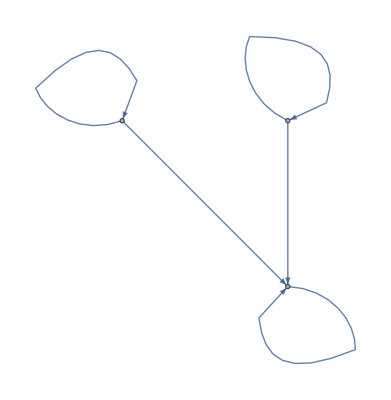
StronglyConnectedComponents[-Graphics-]

StronglyConnectedComponents[Graph[List[1,2,3],List[DirectedEdge[1,1],DirectedEdge[1,3],DirectedEdge[2,2],DirectedEdge[2,3],DirectedEdge[3,3]]]]

```mathematica
(*1. confirm your graph is a Graph object*)Head[g]/. g->Graph[{1,2,3},{DirectedEdge[1,1],DirectedEdge[1,3],DirectedEdge[2,2],DirectedEdge[2,3],DirectedEdge[3,3]}]

(*2. show vertex list and type*)
g=Graph[{1,2,3},{DirectedEdge[1,1],DirectedEdge[1,3],DirectedEdge[2,2],DirectedEdge[2,3],DirectedEdge[3,3]}];
VertexList[g]
Head/@VertexList[g]

(*3. compute SCC and inspect full form*)
scc=StronglyConnectedComponents[g];
scc
FullForm[scc]
```

```mathematica
ClearAll[StronglyConnectedComponents,VertexIndex,g,scc,perm];
g=Graph[{1,2,3},{DirectedEdge[1,1],DirectedEdge[1,3],DirectedEdge[2,2],DirectedEdge[2,3],DirectedEdge[3,3]}];
VertexList[g]
scc=StronglyConnectedComponents[g];FullForm[scc]
perm=Flatten[VertexIndex[g,#]&/@scc];
IntegerQ/@perm
perm
```

ClearAll::wrsym: Symbol VertexIndex is Protected.

{1,2,3}

StronglyConnectedComponents[Graph[List[1,2,3],List[DirectedEdge[1,1],DirectedEdge[1,3],DirectedEdge[2,2],DirectedEdge[2,3],DirectedEdge[3,3]]]]

VertexIndex::inv: The argument … in VertexIndex[Graph[<3>, <5>], Graph[<3>, <5>]] is not a valid vertex.

StronglyConnectedComponents[False]

StronglyConnectedComponents[VertexIndex[-Graphics-,-Graphics-]]

```mathematica
(*do NOT ClearAll protected built-ins;call the system symbols explicitly*)g=Graph[{1,2,3},{DirectedEdge[1,1],DirectedEdge[1,3],DirectedEdge[2,2],DirectedEdge[2,3],DirectedEdge[3,3]}];

scc=System`StronglyConnectedComponents[g];    (*force system function*)
FullForm[scc]
perm=Flatten[System`VertexIndex[g,#]&/@scc];  (*force system VertexIndex*)
IntegerQ/@perm
perm
```

StronglyConnectedComponents::shdw: Symbol StronglyConnectedComponents appears in multiple contexts {System`,Global`}; definitions in context System` may shadow or be shadowed by other definitions.

StronglyConnectedComponents[Graph[List[1,2,3],List[DirectedEdge[1,1],DirectedEdge[1,3],DirectedEdge[2,2],DirectedEdge[2,3],DirectedEdge[3,3]]]]

VertexIndex::inv: The argument … in VertexIndex[Graph[<3>, <5>], Graph[<3>, <5>]] is not a valid vertex.

StronglyConnectedComponents[False]

StronglyConnectedComponents[VertexIndex[-Graphics-,-Graphics-]]

```mathematica
(*remove any user-defined shadowing symbols in Global`*)If[NameQ["Global`StronglyConnectedComponents"],Remove["Global`StronglyConnectedComponents"]];
If[NameQ["Global`VertexIndex"],Remove["Global`VertexIndex"]];

(*then force the system functions and compute the permutation*)
g=Graph[{1,2,3},{DirectedEdge[1,1],DirectedEdge[1,3],DirectedEdge[2,2],DirectedEdge[2,3],DirectedEdge[3,3]}];

scc=System`StronglyConnectedComponents[g];    (*should evaluate to a List of Lists*)
FullForm[scc]
perm=Flatten[System`VertexIndex[g,#]&/@scc];
IntegerQ/@perm
perm
```

StronglyConnectedComponents[Graph[List[1,2,3],List[DirectedEdge[1,1],DirectedEdge[1,3],DirectedEdge[2,2],DirectedEdge[2,3],DirectedEdge[3,3]]]]

VertexIndex::inv: The argument … in VertexIndex[Graph[<3>, <5>], Graph[<3>, <5>]] is not a valid vertex.

StronglyConnectedComponents[False]

StronglyConnectedComponents[VertexIndex[-Graphics-,-Graphics-]]

```mathematica
g=Graph[{1,2,3},{1->1,1->3,2->2,2->3,3->3},DirectedEdges->True];
StronglyConnectedComponents[g]
```

StronglyConnectedComponents[-Graphics-]

```mathematica
g=System`Graph[{1,2,3},{1->1,1->3,2->2,2->3,3->3},DirectedEdges->True];
System`StronglyConnectedComponents[g]
```

StronglyConnectedComponents[-Graphics-]

```mathematica
expression=(a Nb^2)/2+c^2 f$K^2 my$i$Re mz$i$Im Cos[θ]^2+1/2 I bN$f c f$K my$i$Im Cos[θ] Sin[θ]-1/2 I bN$i c f$K my$i$Im Cos[θ] Sin[θ]+1/2 bN$f c f$K my$i$Re Cos[θ] Sin[θ]+1/2 bN$i c f$K my$i$Re Cos[θ] Sin[θ]+c^2 f$K^2 mx$i$Re mz$i$Im Cos[θ] Sin[θ]+1/2 I bN$f c f$K mx$i$Im Sin[θ]^2-1/2 I bN$i c f$K mx$i$Im Sin[θ]^2+1/2 bN$f c f$K mx$i$Re Sin[θ]^2+1/2 bN$i c f$K mx$i$Re Sin[θ]^2+1/2 c^2 f$K^2 my$i$Im^2 Cos[θ]^2 Sin[θ]^2+1/2 c^2 f$K^2 my$i$Re^2 Cos[θ]^2 Sin[θ]^2+c^2 f$K^2 mx$i$Im my$i$Im Cos[θ] Sin[θ]^3+c^2 f$K^2 mx$i$Re my$i$Re Cos[θ] Sin[θ]^3+1/2 c^2 f$K^2 mx$i$Im^2 Sin[θ]^4+1/2 c^2 f$K^2 mx$i$Re^2 Sin[θ]^4;
```